# Bitcoin ROI performance

```mathematica
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

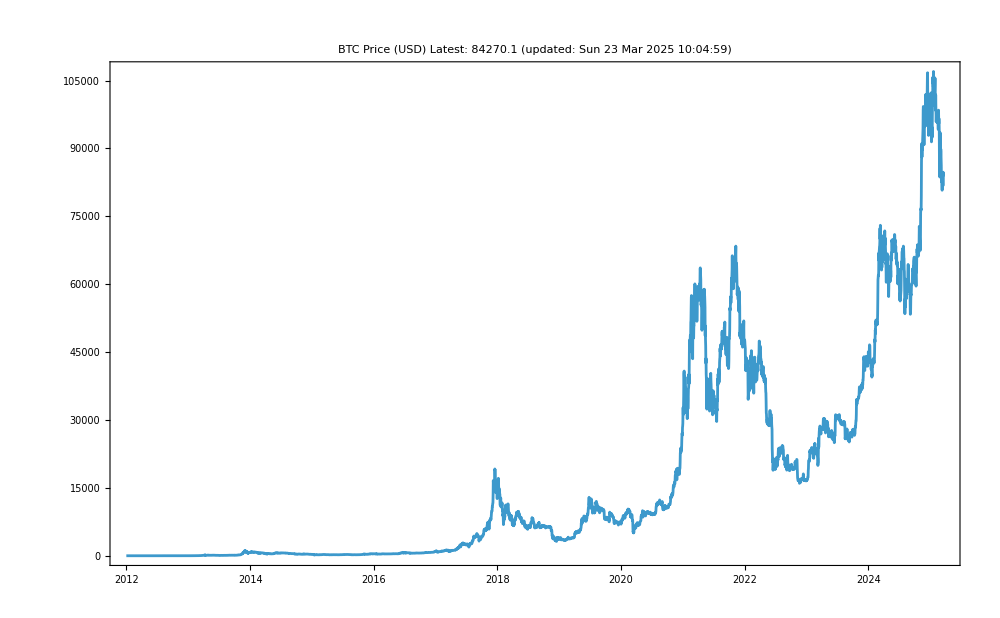

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
btc=FinancialData["BTC/USD",{2012,1,1}];
btcn=btc//Normal;
price = Last[Last[btcn]];
intermediate={#[[1]],#[[2]],UnitConvert[Today-#[[1]],"Years"],1+(price - #[[2]])/(#[[2]])}&/@btcn;
roi={#[[1]],(#[[4]]^(1/QuantityMagnitude[#[[3]]]))-1}&/@ Drop[intermediate,-1];
pl[x_]:=Style[x,{16,Bold,Red}]
settings=<|
drop->180
,imagesize->1000
,ticksstyle->Directive[{16}]
,imagemargins->20
,labelstyle->Directive[14]
,titlestyle->{20,Red}
,subtitlestyle -> {15}
|>;
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],subtitlestyle];

DateListPlot[
btc
,PlotLabel->Column[{
Style["BTC Price (USD)",settings[titlestyle]]
,Style[StringForm["Latest: ``", ToString[btc["LastValue"]]],settings[subtitlestyle]]
,updatedstr
},
Center
]
,GridLines->{Automatic,Range[0,1000000,5000]}
,ImageSize->settings[imagesize]
,FrameTicks->All
,FrameTicksStyle-> settings[ticksstyle]
]
```

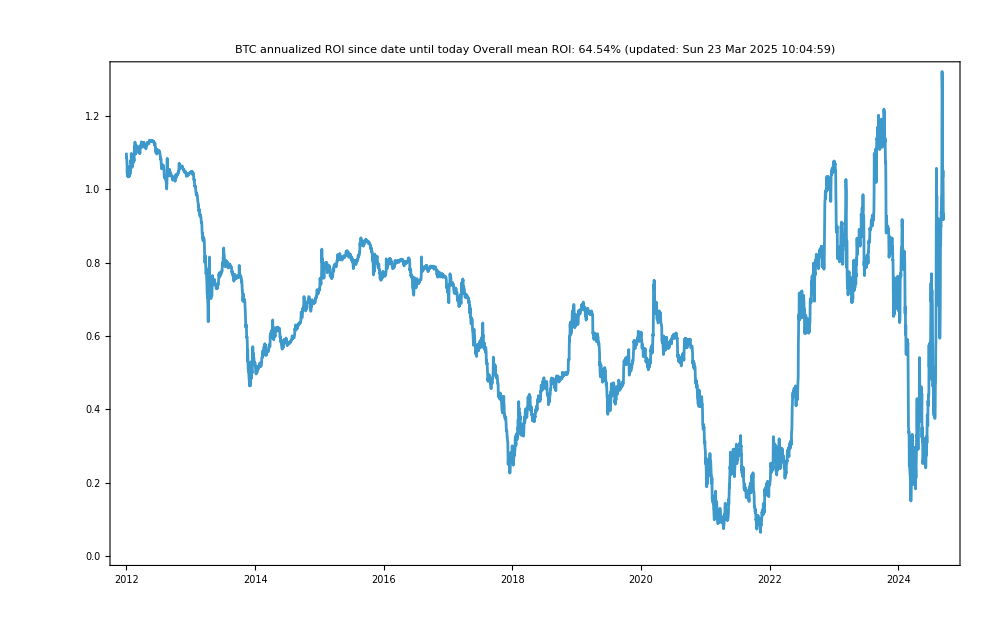

```mathematica
plotdata = Drop[roi,-settings[drop]];
overallmean=Last/@plotdata//Mean;
btcroiperformance=DateListPlot[plotdata
,PlotLabel->Column[{
Style["BTC annualized ROI since date until today",settings[titlestyle]]
,StringForm["Overall mean ROI: ``",PercentForm[overallmean]]
,updatedstr
}
,Center
]
,GridLines->{Automatic, Join[Range[-5,50,0.1],{#,Thick}&/@ Range[0,50,0.5]]}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
, PlotRange->Full
, FrameTicks->All
,FrameTicksStyle-> settings[ticksstyle]
];
filename = "BTC-ROI-Performance.jpg";
Export[filename,btcroiperformance];
btcroiperformance
```

```mathematica
yrs=GroupBy[plotdata,DateValue[First[#],"Year"]&];
yravg=AssociationThread[DateObject[{#}]&/@Keys[yrs] -> Table[Last/@ yrs[yr]//Mean,{yr,Keys[yrs]}]];
btcyearlyroiperformance=DateListPlot[
Callout[#,PercentForm[Last[#]]]&/@KeyValueMap[List,yravg]
,PlotLabel->Column[{
Style["BTC average ROI, bought year to today", settings[titlestyle]]
,Style[StringForm["Overall mean ROI: ``",PercentForm[overallmean]],subtitlestyle]
,updatedstr
},
Center
]
,Joined->False
,GridLines->{
DateRange[DateObject[{2010,1,1}],DateObject[{2030,1,1}], {1, "Year"}] 
,Join[Range[-5,50,0.1],{#,Thick}&/@ Range[0,50,0.1]]
}
,Frame->True
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,PlotRange->Full
,FrameTicks->{Automatic,Table[{x,Style[PercentForm[x],{11}]},{x,0,5,0.1}]}
,FrameTicksStyle-> settings[ticksstyle]
];
filename = "BTC-Yearly-ROI-Performance.jpg";
Export[filename,btcyearlyroiperformance];
btcyearlyroiperformance
```

-Graphics-